# Project 10

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

{{1,0.31},{2,0.32},{3,0.56},{4,0.17},{5,0.36},{6,0.43},{7,0.46},{8,0.36},{9,0.27},{10,0.56},{11,0.25},{12,0.34},{13,0.6},{14,0.51},{15,0.34},{16,0.47},{17,0.71},{18,0.72},{19,0.61},{20,0.65},{21,0.51},{22,0.92},{23,0.27},{24,0.6},{25,0.73},{26,0.47},{27,0.44},{28,0.62},{29,0.7},{30,0.83},{31,1.12},{32,0.98},{33,0.76},{34,0.94},{35,1.15}}

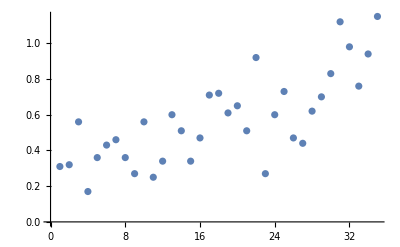

```mathematica
xi=Table[{},2021-1986];
For[i=1,i≤35,i++,
xi[[i]]=i
];
xi
fxi = {0.31,0.32,0.56,0.17,0.36,0.43,0.46,0.36,0.27,0.56,0.25,0.34,0.60,0.51,0.34,0.47,0.71,0.72,0.61,0.65,0.51,0.92,0.27,0.60,0.73,0.47,0.44,0.62,0.70,0.83,1.12,0.98,0.76,0.94,1.15};
(*Just a check to see if we have the same amount of data points and defining a vcariable for the legnth of the vectors*)
n=Length[xi];
Length[fxi];
Orderedpairs=Table[{},2021-1986];
For[i=1,i≤n,i++,
Orderedpairs[[i]]={xi[[i]],fxi[[i]]}
];
Orderedpairs
(*Graphing the Points*)
ListPlot[Orderedpairs]
```

## Numerical Differentiation with the Taylor Theorem

```mathematica
f[x_]:= xi[[1]]+derivfxi[[1]]((x-xi[[1]])/2)
derivfxi=Table[{},n];
Sderivfxi = Table[{},n];
h=xi[[2]]-xi[[1]];

For[i=3,i≤n-2,i++,                  
derivfxi[[i]]=
(fxi[[i-2]]-8fxi[[i-1]]+
8fxi[[i+1]]-fxi[[i+2]])/(12h)]

For[i=1,i≤2,i++, 
derivfxi[[i]]=
(−25fxi[[i]]+48fxi[[i+1]]−36fxi[[i+2]]+
16fxi[[i+3]]−3fxi[[i+4]])(1/(12h))]
For[i=n,i≥n-1,i--, 
derivfxi[[i]]=
(−25fxi[[i]]+48fxi[[i-1]]−36fxi[[i-2]]+
16fxi[[i-3]]−3fxi[[i-4]])(1/(12(-h)))]

derivfxi

(*For loops to tanspose the derivative values into the Table*)
For[i=3,i≤n-2,i++,                  
Sderivfxi[[i]]=
(derivfxi[[i-2]]-8derivfxi[[i-1]]+
8derivfxi[[i+1]]-derivfxi[[i+2]])/(12h)]
For[i=1,i≤2,i++, 
Sderivfxi[[i]]=
(−25derivfxi[[i]]+48derivfxi[[i+1]]−36derivfxi[[i+2]]+
16derivfxi[[i+3]]−3derivfxi[[i+4]])(1/(12h))]
For[i=n,i≥n-1,i--, 
Sderivfxi[[i]]=
(−25derivfxi[[i]]+48derivfxi[[i-1]]−36derivfxi[[i-2]]+
16derivfxi[[i-3]]−3derivfxi[[i-4]])(1/(12(-h)))]
Sderivfxi
```

{-0.909167,1.43583,-0.104167,-0.1425,0.181667,0.0508333,-0.0391667,-0.1375,0.150833,-0.0116667,-0.174167,0.2375,0.105833,-0.184167,-0.0358333,0.229167,0.144167,-0.0816667,-0.03,-0.0833333,0.208333,-0.155833,-0.231667,0.344167,-0.100833,-0.195,0.1025,0.143333,0.0833333,0.25,0.095,-0.249167,-0.0291667,0.5725,-0.110833}

{7.71451,-2.75097,-1.14313,0.305972,0.123472,-0.147639,-0.122986,0.131875,0.0951389,-0.247917,0.169861,0.201042,-0.292639,-0.09375,0.272361,0.111458,-0.207708,-0.0900694,-0.00645833,0.165069,-0.0315278,-0.328958,0.359097,0.0904861,-0.387292,0.152292,0.210208,-0.0498611,0.0717361,0.0404861,-0.323403,-0.109653,0.564931,0.497708,-2.25243}

## Making Taylor Polynomial

```mathematica
Allptay = Table[ {}, n] ;
For[ i=1, i≤ n, i++,
Allptay[[i]] = fxi[[i]] + derivfxi[[i]]((x-xi[[i]])/i!)+Sderivfxi[[i]]((x-xi[[i]])^(2)/i!)
]
Simplify[Allptay];
Taylorpol[x_] = Simplify[Allptay[[1]]];
Taylorpol[xi]
```

{0.31,7.11535,29.3497,67.0131,120.106,188.627,272.578,371.957,486.766,617.003,762.67,923.765,1100.29,1292.24,1499.63,1722.44,1960.68,2214.35,2483.45,2767.98,3067.93,3383.32,3714.13,4060.38,4422.05,4799.15,5191.68,5599.64,6023.03,6461.85,6916.1,7385.77,7870.88,8371.41,8887.38}

## Error For Taylor Polynomial

{1.38778×10^-15,6.79535,28.7897,66.8431,119.746,188.197,272.118,371.597,486.496,616.443,762.42,923.425,1099.69,1291.73,1499.29,1721.97,1959.97,2213.63,2482.84,2767.33,3067.42,3382.4,3713.86,4059.78,4421.32,4798.68,5191.24,5599.02,6022.33,6461.02,6914.98,7384.79,7870.12,8370.47,8886.23}

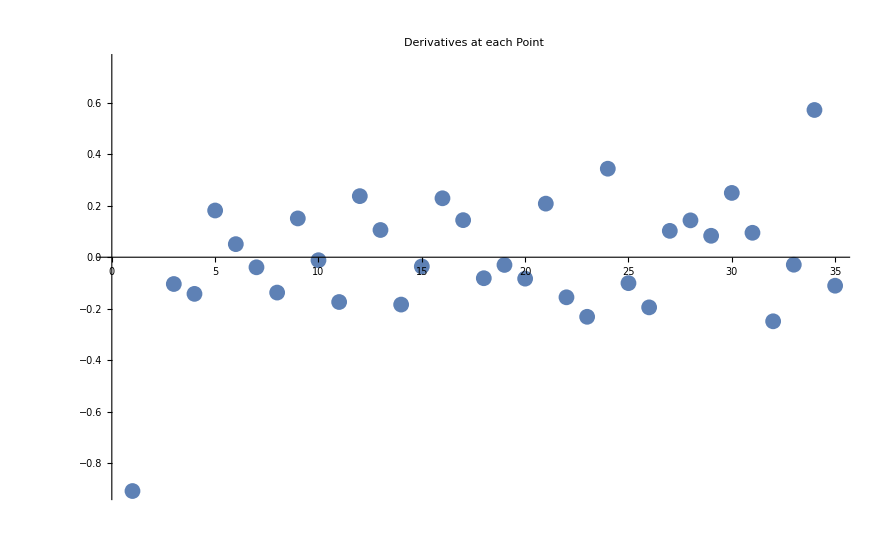

```mathematica
Tayerr  = Table[{},n];
For[i=1,i≤35,i++,
Tayerr[[i]]= Abs[fxi[[i]]-Taylorpol[xi[[i]]]]
]
Tayerr
m1=Transpose[{xi,derivfxi}];
ListPlot[m1,PlotLabel->"Derivatives at each Point"]
ListPlot[Orderedpairs];
```

## Making the Lagrange Interpolating Polynomial

## Making the Lagrange Interpolating Polynomial

```mathematica
Spacing = xi[[2]]-xi[[1]];
LagVar=Table[{},n];
```

```mathematica
(*Making the divided difference table*)
MatrixForm[DivDif = Table[{},n,n]];
For[i=1,i≤ n, i++,
DivDif[[i,1]] = fxi[[i]]]

For[ j=2,j≤ n, j++,
For[i=j,i≤ n, i++,
DivDif[[i,j]]=(DivDif[[i,j-1]]-DivDif[[i-1,j-1]])/
((xi[[i]])-(xi[[i-(j-1)]]))]]
MatrixForm[DivDif];
```

```mathematica
LagPol[x_]:=Sum[DivDif[[i,i]]*Product[(x-xi[[j]]),{j,1,i-1}],{i,1,n}]
Simplify[LagPol[x]]
LagPol[xi]
```

-1.14249×10^9+4.68372×10^9 x-8.67843×10^9 x^2+9.79642×10^9 x^3-7.63548×10^9 x^4+4.40596×10^9 x^5-1.96804×10^9 x^6+7.01807×10^8 x^7-2.04348×10^8 x^8+4.94176×10^7 x^9-1.00573×10^7 x^10+1.74048×10^6 x^11-258242. x^12+33066.8 x^13-3672.9 x^14+355.317 x^15-30.027 x^16+2.22126 x^17-0.144016 x^18+0.00818699 x^19-0.000407898 x^20+0.0000177882 x^21-6.77478×10^-7 x^22+2.24597×10^-8 x^23-6.45184×10^-10 x^24+1.59623×10^-11 x^25-3.37419×10^-13 x^26+6.03032×10^-15 x^27-8.98544×10^-17 x^28+1.0953×10^-18 x^29-1.06354×10^-20 x^30+7.90884×10^-23 x^31-4.2283×10^-25 x^32+1.4465×10^-27 x^33-2.37772×10^-30 x^34

{0.31,0.32,0.56,0.17,0.36,0.43,0.46,0.36,0.27,0.56,0.25,0.34,0.6,0.51,0.34,0.47,0.71,0.72,0.61,0.65,0.51,0.92,0.27,0.6,0.73,0.47,0.439999,0.619991,0.699966,0.829926,1.11993,0.978516,0.759766,0.933594,1.13867}

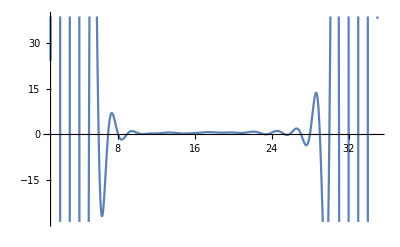

```mathematica
Plot[LagPol[x],{x,1,n}]
```

## Lagrange Error

```mathematica
LagErr = Table[{},n];
For[i=1,i≤35,i++,
LagErr[[i]]= Abs[fxi[[i]]-LagPol[xi[[i]]]]
]
LagErr
```

{0.,0.,0.,1.38778×10^-16,1.11022×10^-16,2.77556×10^-16,5.38458×10^-15,3.07532×10^-14,7.68274×10^-14,1.71863×10^-13,1.06581×10^-13,2.59515×10^-13,7.58282×10^-14,8.90177×10^-13,7.02355×10^-12,2.02636×10^-11,1.73168×10^-11,7.43239×10^-11,4.48926×10^-11,6.13363×10^-10,9.07457×10^-10,8.61299×10^-9,4.60248×10^-9,5.57397×10^-8,2.7083×10^-7,1.16213×10^-7,3.69298×10^-6,0.0000134999,0.0000346699,0.0000745346,0.0000682556,0.00120289,0.0000528598,0.00746221,0.0124535}

## Derivatives according to Lagrange Interpolation

```mathematica
LagDer[x_] = Simplify[D[LagPol[x],x]]
LagDer[xi]
```

4.68372×10^9-1.73569×10^10 x+2.93893×10^10 x^2-3.05419×10^10 x^3+2.20298×10^10 x^4-1.18082×10^10 x^5+4.91265×10^9 x^6-1.63478×10^9 x^7+4.44759×10^8 x^8-1.00573×10^8 x^9+1.91453×10^7 x^10-3.0989×10^6 x^11+429868. x^12-51420.6 x^13+5329.75 x^14-480.432 x^15+37.7614 x^16-2.59229 x^17+0.155553 x^18-0.00815796 x^19+0.000373553 x^20-0.0000149045 x^21+5.16573×10^-7 x^22-1.54844×10^-8 x^23+3.99057×10^-10 x^24-8.77289×10^-12 x^25+1.62819×10^-13 x^26-2.51592×10^-15 x^27+3.17636×10^-17 x^28-3.19063×10^-19 x^29+2.45174×10^-21 x^30-1.35306×10^-23 x^31+4.77346×10^-26 x^32-8.08425×10^-29 x^33

{3.42631×10^7,-1.06064×10^6,67869.3,-6743.31,926.679,-165.477,36.625,-10.,12.,0.,0.,0.,2048.,-8192.,-32768.,65536.,131072.,1.57286×10^6,-4.1943×10^6,1.04858×10^7,1.67772×10^7,-2.51658×10^7,-1.67772×10^7,3.35544×10^7,6.0398×10^8,5.36871×10^8,3.22123×10^9,-3.7581×10^9,-8.58993×10^9,2.14748×10^9,1.50324×10^10,-1.28849×10^10,6.01295×10^10,3.43597×10^10,5.15396×10^10}

## Creating the Spline

```mathematica
d= Length[xi];
hi = Table[{}, Length[xi]-1];
For[i=1, i≤ Length[xi]-1,i++,
hi[[i]] = xi[[i+1]]-xi[[i]]]
hi;
(*Creating a Matrix to put our known variables in*)
aMatrix = Table[{},d-2,d-2];
MatrixForm[aMatrix];

For[ j=1,j≤ d-2, j++,
For[i=1,i≤ d-2, i++,
aMatrix[[i,j]] = 0
]
]

(*First diagonal (i)*)
For[ j=2,j≤ d-2, j++,
For[i=j-1,i≤ j-1, i++,
aMatrix[[i,j]] = hi[[i+1]]
]
]

(*Middle diagonal (i)*)
For[ j=1,j≤ d-2, j++,
For[i=j,i≤ j, i++,
aMatrix[[i,j]] = (2(hi[[i]]+hi[[i+1]]))
]
]
(*Bottom Diagonal (i-1)*)
For[ j=1,j≤ d-3, j++,
For[i=j+1,i≤ j+1, i++,
aMatrix[[i,j]] = hi[[i]]
]
]


(*Matrix A to solve for cj*)
MatrixForm[aMatrix];
(*Matrix b to solve for cj's*)
bMatrix = Table[{},d-2,1];
For[i=2,i≤ d-1, i++,
bMatrix[[i-1]] = ((3/hi[[i]])(fxi[[i+1]]-fxi[[i]]))-((3/hi[[i-1]])(fxi[[i]]-fxi[[i-1]]))
]

(*Correct Matrix for b*)
MatrixForm[bMatrix];
cj=LinearSolve[aMatrix,bMatrix];
(*Do not redo this Function or else to many variables in cj*)
PrependTo[cj,0];
AppendTo[cj,0];
cj;
(*Creating the bj Mat*)
bj = Table[{},d-1,1];
MatrixForm[bj];
(*Filling bj matrix with proper values*)
For[i=1,i≤d-1, i++,
bj[[i]] = ((fxi[[i+1]]-fxi[[i]])/hi[[i]])-((hi[[i]]/3)(2cj[[i]]+cj[[i+1]]))
]
bj;
(*Making a Matrix for dj*)
dj = Table[{},d-1,1];
MatrixForm[dj];
For[i=1,i≤d-1, i++,
dj[[i]] = (1/(3hi[[i]]))(cj[[i+1]]-cj[[i]])
]
dj;
```

```mathematica
SplineFuncs3 = Table[{}, d-1];
For[i= 1, i≤ d-1, i++,
SplineFuncs3[[i]] = fxi[[i]] + bj[[i]](x-xi[[i]])+ cj[[i]](x-xi[[i]])^2 + dj[[i]](x-xi[[i]])^3
]
MatrixForm[SplineFuncs3];
Remove[Wild2]

Wild2[x_] := Piecewise[ {
{SplineFuncs3[[1]], xi[[1]] ≤ x ≤ xi[[2]]},
{SplineFuncs3[[2]],  xi[[2]] ≤ x ≤ xi[[3]]},
{SplineFuncs3[[3]],  xi[[3]] ≤ x ≤ xi[[4]]},
{SplineFuncs3[[4]],  xi[[4]] ≤ x ≤ xi[[5]]},
{SplineFuncs3[[5]],  xi[[5]] ≤ x ≤ xi[[6]]},
{SplineFuncs3[[6]],  xi[[6]] ≤ x ≤ xi[[7]]},
{SplineFuncs3[[7]],  xi[[7]] ≤ x ≤ xi[[8]]},
{SplineFuncs3[[8]],  xi[[8]] ≤ x ≤ xi[[9]]},
{SplineFuncs3[[9]],  xi[[9]] ≤ x ≤ xi[[10]]},
{SplineFuncs3[[10]],  xi[[10]] ≤ x ≤ xi[[11]]},
{SplineFuncs3[[11]],  xi[[11]] ≤ x ≤ xi[[12]]},
{SplineFuncs3[[12]],  xi[[12]] ≤ x ≤ xi[[13]]},
{SplineFuncs3[[13]],  xi[[13]] ≤ x ≤ xi[[14]]},
{SplineFuncs3[[14]],  xi[[14]] ≤ x ≤ xi[[15]]},
{SplineFuncs3[[15]],  xi[[15]] ≤ x ≤ xi[[16]]},
{SplineFuncs3[[16]],  xi[[16]] ≤ x ≤ xi[[17]]},
{SplineFuncs3[[17]],  xi[[17]] ≤ x ≤ xi[[18]]},
{SplineFuncs3[[18]],  xi[[18]] ≤ x ≤ xi[[19]]},
{SplineFuncs3[[19]],  xi[[19]] ≤ x ≤ xi[[20]]},
{SplineFuncs3[[20]],  xi[[20]] ≤ x ≤ xi[[21]]},
{SplineFuncs3[[21]],  xi[[21]] ≤ x ≤ xi[[22]]},
{SplineFuncs3[[22]],  xi[[22]] ≤ x ≤ xi[[23]]},
{SplineFuncs3[[23]],  xi[[23]] ≤ x ≤ xi[[24]]},
{SplineFuncs3[[24]],  xi[[24]] ≤ x ≤ xi[[25]]},
{SplineFuncs3[[25]],  xi[[25]] ≤ x ≤ xi[[26]]},
{SplineFuncs3[[26]],  xi[[26]] ≤ x ≤ xi[[27]]},
{SplineFuncs3[[27]],  xi[[27]] ≤ x ≤ xi[[28]]},
{SplineFuncs3[[28]],  xi[[28]] ≤ x ≤ xi[[29]]},
{SplineFuncs3[[29]],  xi[[29]] ≤ x ≤ xi[[30]]},
{SplineFuncs3[[30]],  xi[[30]] ≤ x ≤ xi[[31]]},
{SplineFuncs3[[31]],  xi[[31]] ≤ x ≤ xi[[32]]},
{SplineFuncs3[[32]],  xi[[32]] ≤ x ≤ xi[[33]]},
{SplineFuncs3[[33]],  xi[[33]] ≤ x ≤ xi[[34]]},
{SplineFuncs3[[34]],  xi[[34]] ≤ x ≤ xi[[35]]}
}]
Wild2[x]
```

Piecewise[{{0.31-0.108616 (-1+x)+0.118616 (-1+x)^3, 1≤x≤2}, {0.32+0.247231 (-2+x)+0.355847 (-2+x)^2-0.363078 (-2+x)^3, 2≤x≤3}, {0.56-0.13031 (-3+x)-0.733388 (-3+x)^2+0.473698 (-3+x)^3, 3≤x≤4}, {0.17-0.175992 (-4+x)+0.687706 (-4+x)^2-0.321713 (-4+x)^3, 4≤x≤5}, {0.36+0.234279 (-5+x)-0.277434 (-5+x)^2+0.113155 (-5+x)^3, 5≤x≤6}, {0.43+0.0188758 (-6+x)+0.0620307 (-6+x)^2-0.0509066 (-6+x)^3, 6≤x≤7}, {0.46-0.00978236 (-7+x)-0.0906889 (-7+x)^2+0.000471286 (-7+x)^3, 7≤x≤8}, {0.36-0.189746 (-8+x)-0.0892751 (-8+x)^2+0.189021 (-8+x)^3, 8≤x≤9}, {0.27+0.198768 (-9+x)+0.477789 (-9+x)^2-0.386557 (-9+x)^3, 9≤x≤10}, {0.56-0.00532471 (-10+x)-0.681882 (-10+x)^2+0.377206 (-10+x)^3, 10≤x≤11}, {0.25-0.237469 (-11+x)+0.449737 (-11+x)^2-0.122268 (-11+x)^3, 11≤x≤12}, {0.34+0.2952 (-12+x)+0.082932 (-12+x)^2-0.118132 (-12+x)^3, 12≤x≤13}, {0.6+0.106667 (-13+x)-0.271465 (-13+x)^2+0.0747984 (-13+x)^3, 13≤x≤14}, {0.51-0.211869 (-14+x)-0.0470702 (-14+x)^2+0.0889388 (-14+x)^3, 14≤x≤15}, {0.34-0.0391926 (-15+x)+0.219746 (-15+x)^2-0.0505537 (-15+x)^3, 15≤x≤16}, {0.47+0.248639 (-16+x)+0.0680851 (-16+x)^2-0.0767239 (-16+x)^3, 16≤x≤17}, {0.71+0.154637 (-17+x)-0.162087 (-17+x)^2+0.0174495 (-17+x)^3, 17≤x≤18}, {0.72-0.117188 (-18+x)-0.109738 (-18+x)^2+0.116926 (-18+x)^3, 18≤x≤19}, {0.61+0.0141138 (-19+x)+0.24104 (-19+x)^2-0.215154 (-19+x)^3, 19≤x≤20}, {0.65-0.149268 (-20+x)-0.404421 (-20+x)^2+0.413689 (-20+x)^3, 20≤x≤21}, {0.51+0.282956 (-21+x)+0.836645 (-21+x)^2-0.709601 (-21+x)^3, 21≤x≤22}, {0.92-0.172558 (-22+x)-1.29216 (-22+x)^2+0.814717 (-22+x)^3, 22≤x≤23}, {0.27-0.312725 (-23+x)+1.15199 (-23+x)^2-0.509267 (-23+x)^3, 23≤x≤24}, {0.6+0.463459 (-24+x)-0.375808 (-24+x)^2+0.0423492 (-24+x)^3, 24≤x≤25}, {0.73-0.161109 (-25+x)-0.24876 (-25+x)^2+0.14987 (-25+x)^3, 25≤x≤26}, {0.47-0.209021 (-26+x)+0.200849 (-26+x)^2-0.0218282 (-26+x)^3, 26≤x≤27}, {0.44+0.127193 (-27+x)+0.135364 (-27+x)^2-0.0825569 (-27+x)^3, 27≤x≤28}, {0.62+0.150251 (-28+x)-0.112306 (-28+x)^2+0.0420557 (-28+x)^3, 28≤x≤29}, {0.7+0.0518051 (-29+x)+0.0138608 (-29+x)^2+0.064334 (-29+x)^3, 29≤x≤30}, {0.83+0.272529 (-30+x)+0.206863 (-30+x)^2-0.189392 (-30+x)^3, 30≤x≤31}, {1.12+0.118079 (-31+x)-0.361313 (-31+x)^2+0.103233 (-31+x)^3, 31≤x≤32}, {0.98-0.294846 (-32+x)-0.0516127 (-32+x)^2+0.126459 (-32+x)^3, 32≤x≤33}, {0.76-0.0186953 (-33+x)+0.327763 (-33+x)^2-0.129068 (-33+x)^3, 33≤x≤34}, {0.94+0.249627 (-34+x)-0.0594408 (-34+x)^2+0.0198136 (-34+x)^3, 34≤x≤35}, {0, True}}]

## Creating the Hermite

```mathematica
m=2*Length[xi];
MatrixForm[DivDif2=Table[{},m,m+1]];

For[i=1,i≤m/2,i++,
DivDif2[[(2 i),1]]=xi[[i]]] 
For[i=1,i≤m/2,i++,
DivDif2[[(2i)-1,1]]=xi[[i]]]

For[i=1,i≤m / 2,i++,
DivDif2[[(2i),2]]=fxi[[i]]]
For[i=1,i≤m/2,i++,
DivDif2[[(2i)-1,2]]=fxi[[i]]]

For[ j=2,j≤2,j++,
For[i=j,i≤m,i++,
DivDif2[[i,j+1]]=(DivDif2[[i,j]]-DivDif2[[i-1,j]]) / 
(DivDif2[[i,j-1]]-DivDif2[[i-1,j-1]])
]] 
MatrixForm[DivDif2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
h=xi[[2]]-xi[[1]];
derivfxi=Table[{},n];

For[i=3,i≤n-2,i++,                  
derivfxi[[i]]=
(fxi[[i-2]]-8fxi[[i-1]]+
8fxi[[i+1]]-fxi[[i+2]])/(12h)]
For[i=1,i≤2,i++, 
derivfxi[[i]]=
(−25fxi[[i]]+48fxi[[i+1]]−36fxi[[i+2]]+
16fxi[[i+3]]−3fxi[[i+4]])(1/(12h))]
For[i=n,i≥n-1,i--, 
derivfxi[[i]]=
(−25fxi[[i]]+48fxi[[i-1]]−36fxi[[i-2]]+
16fxi[[i-3]]−3fxi[[i-4]])(1/(12(-h)))]
derivfxi;

For[i=1,i≤m/2,i++,
DivDif2[[(2i),3]]=derivfxi[[i]]]
MatrixForm[DivDif2];

For[ j=3,j≤m,j++,
For[i=j,i≤m,i++,DivDif2[[i,j+1]]=(DivDif2[[i,j]]-DivDif2[[i-1,j]]) / (DivDif2[[i,j-(j-1)]]-DivDif2[[i-(j-1),j-(j-1)]])]]
MatrixForm[DivDif2];

Herm[x_]:=Sum[DivDif2[[i,i+1]]*Product[(x-DivDif2[[j,1]]),{j,1,i-1}],{i,1,m}]
Simplify[Herm[x]]
```

1.0117×10^17-8.25282×10^17 x+3.20273×10^18 x^2-7.90144×10^18 x^3+1.39695×10^19 x^4-1.89125×10^19 x^5+2.04553×10^19 x^6-1.82043×10^19 x^7+1.36242×10^19 x^8-8.71943×10^18 x^9+4.83588×10^18 x^10-2.34938×10^18 x^11+1.00878×10^18 x^12-3.85705×10^17 x^13+1.32159×10^17 x^14-4.08032×10^16 x^15+1.14051×10^16 x^16-2.89806×10^15 x^17+6.71864×10^14 x^18-1.42561×10^14 x^19+2.7764×10^13 x^20-4.97504×10^12 x^21+8.22042×10^11 x^22-1.2549×10^11 x^23+1.77289×10^10 x^24-2.32141×10^9 x^25+2.82087×10^8 x^26-3.18458×10^7 x^27+3.34323×10^6 x^28-326633. x^29+29716.1 x^30-2518.57 x^31+198.913 x^32-14.6405 x^33+1.00413 x^34-0.0641547 x^35+0.00381614 x^36-0.000211156 x^37+0.0000108551 x^38-5.17564×10^-7 x^39+2.28336×10^-8 x^40-9.29013×10^-10 x^41+3.46935×10^-11 x^42-1.18076×10^-12 x^43+3.62097×10^-14 x^44-9.80634×10^-16 x^45+2.25009×10^-17 x^46-3.9051×10^-19 x^47+2.61056×10^-21 x^48+1.56475×10^-22 x^49-9.38003×10^-24 x^50+3.38943×10^-25 x^51-9.74978×10^-27 x^52+2.39342×10^-28 x^53-5.14966×10^-30 x^54+9.82507×10^-32 x^55-1.67012×10^-33 x^56+2.53149×10^-35 x^57-3.41535×10^-37 x^58+4.08512×10^-39 x^59-4.30601×10^-41 x^60+3.96705×10^-43 x^61-3.15955×10^-45 x^62+2.14407×10^-47 x^63-1.21564×10^-49 x^64+5.60368×10^-52 x^65-2.01773×10^-54 x^66+5.32409×10^-57 x^67-9.15678×10^-60 x^68+7.70308×10^-63 x^69

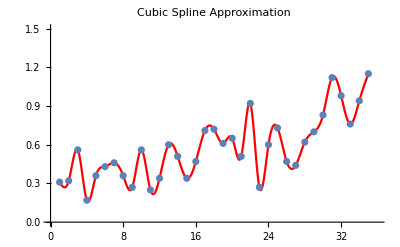

```mathematica
Show[
Plot[Wild2[x],{x,1,35}, PlotLabel->"Cubic Spline Approximation", PlotStyle->Red, PlotRange -> {{0,36},{0,1.5}}, PlotLegends->"Cubic Spline"],
ListPlot[Orderedpairs]
]
```

## Project 8 code for Project 6

```mathematica
howmany3 = n;
hstep3 = (xi[[n]]-xi[[1]])/(howmany3-1);
points3 = howmany3;
xip8c = Table[ xi[[i]], {i, 1, points3 }];
fxip8c = Table[{},{points3 }];
For[i=1, i≤ points3, i++,
fxip8c[[i]] = fxi[[i]]
]
fxip8c;

TrapInt3 = ( fxi[[1]] 
+ fxi[[n]] 
+ 2*Sum[fxi[[i+1]],{i,1,points3-2}])(hstep3/2);
N[TrapInt3]
```

19.31

```mathematica
howmany4 = n;
hstep4 = (xi[[n]]-xi[[1]])/(howmany4-1);
points4 = howmany4;
xip8d = Table[ xi[[i]], {i, 1, points4 }];
```

```mathematica
fxip8d = Table[{},{points4 }];
For[i=1, i≤ points4, i++,
fxip8d[[i]] = fxi[[i]]
]
fxip8d;
TrapSimp4 = ( fxip8d[[1]] 
+ fxip8d[[points4]] 
+ 2*Sum[fxip8d[[2i-1]],{i,2,(points4-1)/2}]
+ 4*Sum[fxip8d[[2i]],{i,1,(points4-1)/2}])(hstep4/3);
N[TrapSimp4]
```

19.4667

## Using what we Learned from Gaussian Quadrature to pick points for the Lagrange and Hermite

```mathematica
xi2 = {2,4,8,17,25,30,33,35}
fxi2 = {0.32,0.17,0.36,0.71,0.73,0.83, 0.76,1.15}
```

{2,4,8,17,25,30,33,35}

{0.32,0.17,0.36,0.71,0.73,0.83,0.76,1.15}

## Making the Lagrange Interpolating Polynomial with better points

```mathematica
n2= Length[xi2];
LagVar2=Table[{},n2];
```

```mathematica
(*Making the divided difference table*)
MatrixForm[DivDif21 = Table[{},n2,n2]]
For[i=1,i≤ n2, i++,
DivDif21[[i,1]] = fxi2[[i]]]

For[ j=2,j≤ n2, j++,
For[i=j,i≤ n2, i++,
DivDif21[[i,j]]=(DivDif21[[i,j-1]]-DivDif21[[i-1,j-1]])/
((xi2[[i]])-(xi2[[i-(j-1)]]))]]
MatrixForm[DivDif21]
```

({} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {})

(0.32 | {} | {} | {} | {} | {} | {} | {}
0.17 | -0.075 | {} | {} | {} | {} | {} | {}
0.36 | 0.0475 | 0.0204167 | {} | {} | {} | {} | {}
0.71 | 0.0388889 | -0.000662393 | -0.00140527 | {} | {} | {} | {}
0.73 | 0.0025 | -0.00214052 | -0.0000703871 | 0.0000580384 | {} | {} | {}
0.83 | 0.02 | 0.00134615 | 0.000158485 | 8.80279×10^-6 | -1.75842×10^-6 | {} | {}
0.76 | -0.0233333 | -0.00541667 | -0.000422676 | -0.0000232465 | -1.10515×10^-6 | 2.10732×10^-8 | {}
1.15 | 0.195 | 0.0436667 | 0.00490833 | 0.000296167 | 0.0000118301 | 4.17267×10^-7 | 1.20059×10^-8)

```mathematica
LagPol2[x_]:=Sum[DivDif21[[i,i]]*Product[(x-xi2[[j]]),{j,1,i-1}],{i,1,n2}]
Simplify[LagPol2[x]]
LagPol[xi2]
```

0.528147-0.063653 x-0.0420863 x^2+0.0134154 x^3-0.00136017 x^4+0.0000635061 x^5-1.40763×10^-6 x^6+1.20059×10^-8 x^7

{0.32,0.17,0.36,0.71,0.73,0.829926,0.759766,1.13867}

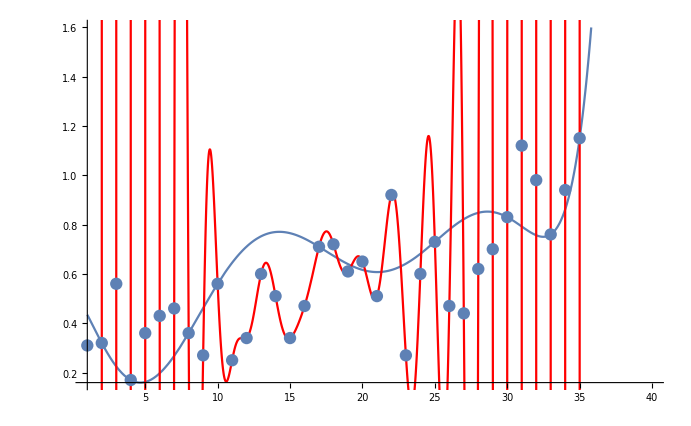

```mathematica
Show[
Plot[LagPol2[x],{x,1,n+5}],
Plot[LagPol[x],{x,1,n+5},PlotStyle->Red],
ListPlot[Orderedpairs]
]
```

```mathematica
LagPol[36]
LagPol2[36]
```

-1.71802×10^9

1.75192

## Creating the Hermite

```mathematica
xi3 = {4,8,12,16,20,24,28,32,36}
fxi3 = {0.17,0.36 ,0.34,0.47,0.65,0.6, 0.62,0.98,1.45}
```

{4,8,12,16,20,24,28,32,36}

{0.17,0.36,0.34,0.47,0.65,0.6,0.62,0.98,1.45}

```mathematica
w = Length[xi3]
m2=2*Length[xi3];
MatrixForm[DivDif3=Table[{},m2,m2+1]];

For[i=1,i≤m2/2,i++,
DivDif3[[(2 i),1]]=xi3[[i]]] 
For[i=1,i≤m2/2,i++,
DivDif3[[(2i)-1,1]]=xi3[[i]]]

For[i=1,i≤m2 / 2,i++,
DivDif3[[(2i),2]]=fxi3[[i]]]
For[i=1,i≤m2/2,i++,
DivDif3[[(2i)-1,2]]=fxi3[[i]]]

For[ j=2,j≤2,j++,
For[i=j,i≤m2,i++,
DivDif3[[i,j+1]]=(DivDif3[[i,j]]-DivDif3[[i-1,j]]) / 
(DivDif3[[i,j-1]]-DivDif3[[i-1,j-1]])
]] 
MatrixForm[DivDif3];
```

9

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
h2=xi3[[2]]-xi3[[1]];
derivfxi3=Table[{},w]

For[i=3,i≤w,i++,                  
derivfxi3[[i]]=
(fxi3[[i-2]]-8fxi3[[i-1]]+
8fxi3[[i+1]]-fxi3[[i+2]])/(12h2)]
For[i=1,i≤2,i++, 
derivfxi3[[i]]=
(−25fxi3[[i]]+48fxi3[[i+1]]−36fxi3[[i+2]]+
16fxi3[[i+3]]−3fxi3[[i+4]])(1/(12h2))]
For[i=w,i≥w-1,i--, 
derivfxi3[[i]]=
(−25fxi3[[i]]+48fxi3[[i-1]]−36fxi3[[i-2]]+
16fxi3[[i-3]]−3fxi3[[i-4]])(1/(12(-h2)))]
derivfxi3

For[i=1,i≤m2/2,i++,
DivDif3[[(2i),3]]=derivfxi3[[i]]]
MatrixForm[DivDif3];

For[ j=3,j≤m2,j++,
For[i=j,i≤m2,i++,DivDif3[[i,j+1]]=(DivDif3[[i,j]]-DivDif3[[i-1,j]]) / (DivDif3[[i,j-(j-1)]]-DivDif3[[i-(j-1),j-(j-1)]])]]
MatrixForm[DivDif3];

Herm2[x_]:=Sum[DivDif3[[i,i+1]]*Product[(x-DivDif3[[j,1]]),{j,1,i-1}],{i,1,m2}]
Simplify[Herm2[x]]
Herm2[xi3]
```

{{},{},{},{},{},{},{},{},{}}

Part::partw: Part 10 of {0.17,0.36,0.34,0.47,0.65,0.6,0.62,0.98,1.45} does not exist.

Part::partw: Part 11 of {0.17,0.36,0.34,0.47,0.65,0.6,0.62,0.98,1.45} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0.1325,-0.0208333,0.00833333,0.0466667,0.0158333,-0.015625,0.0466667,0.153125,0.0808333}

975.205-1282.95 x+753.217 x^2-262.819 x^3+61.2419 x^4-10.1433 x^5+1.23969 x^6-0.114445 x^7+0.00809368 x^8-0.000441605 x^9+0.0000186072 x^10-6.02321×10^-7 x^11+1.47944×10^-8 x^12-2.69734×10^-10 x^13+3.51874×10^-12 x^14-3.08424×10^-14 x^15+1.61191×10^-16 x^16-3.74046×10^-19 x^17

{0.17,0.36,0.34,0.47,0.65,0.6,0.62,0.98,1.45}

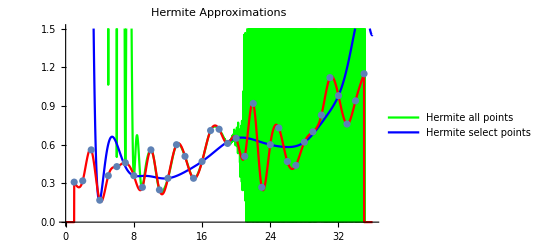

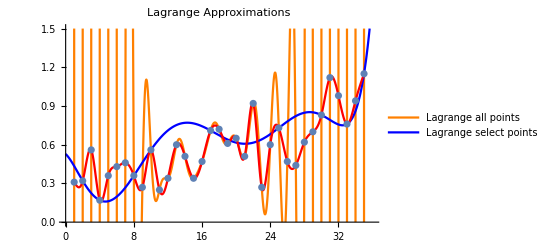

```mathematica
Show[
Plot[{Herm[x]},{x,0,36},PlotLegends-> {"Hermite all points"},PlotLabel->"Hermite Approximations", PlotRange -> {{0,36},{0,1.5}}, PlotStyle->Green],
Plot[{Herm2[x]},{x,0,36},PlotLegends-> {"Hermite select points"}, PlotRange -> {{0,36},{0,1.5}}, PlotStyle->Blue],
Plot[Wild2[x],{x,0,36},PlotLegends-> Automatic, PlotStyle->Red, PlotRange -> {{0,36},{0,1.5}}],
ListPlot[Orderedpairs]
]
Show[
Plot[{LagPol[x]},{x,0,36},PlotLegends-> {"Lagrange all points"},PlotLabel->"Lagrange Approximations", PlotRange -> {{0,36},{0,1.5}}, PlotStyle->Orange],
Plot[{LagPol2[x]},{x,0,36},PlotLegends-> {"Lagrange select points"}, PlotRange -> {{0,36},{0,1.5}}, PlotStyle-> Blue],
Plot[Wild2[x],{x,1,35}, PlotLegends-> Automatic, PlotStyle->Red, PlotRange -> {{0,36},{0,1.5}}],
ListPlot[Orderedpairs]
]
```

## Error for Lagrange

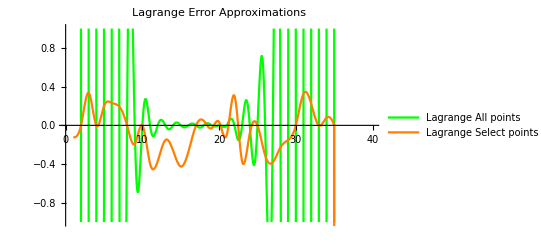

```mathematica
Show[
Plot[Wild2[x]-LagPol[x],{x,1,n+5},PlotRange->{-1,1},PlotLegends-> {"Lagrange All points"},PlotLabel->"Lagrange Error Approximations", PlotStyle->Green],
Plot[Wild2[x]-LagPol2[x],{x,1,n+5},PlotLegends-> {"Lagrange Select points"},PlotLabel->"Lagrange Error Approximations", PlotStyle->Orange]
]
```

## Error For Hermite

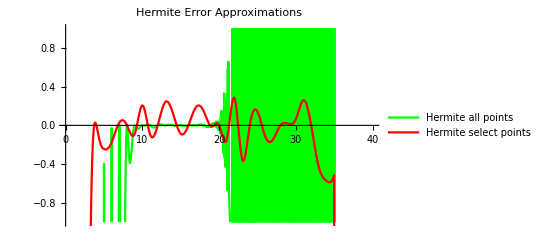

```mathematica
Show[
Plot[Wild2[x]-Herm[x],{x,1,n+5},PlotRange->{-1,1},PlotLegends-> {"Hermite all points"},PlotLabel->"Hermite Error Approximations", PlotStyle->Green],
Plot[Wild2[x]-Herm2[x],{x,1,n+5},PlotLegends-> {"Hermite select points"},PlotLabel->"Hermite Error Approximations", PlotStyle->Red]
]
```